```mathematica
Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]
```

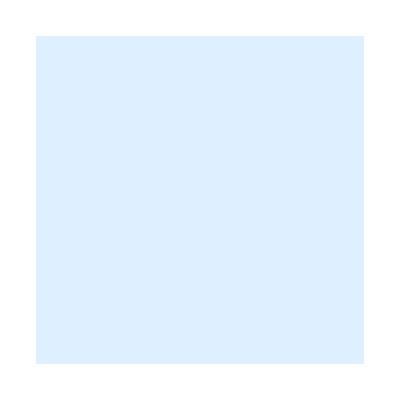

```mathematica
Graphics[{EdgeForm[Thick],LightBlue,Rectangle[{0,0}]}]
```

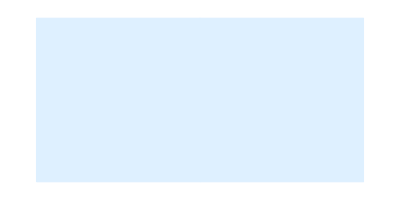

```mathematica
Graphics[{EdgeForm[Thick],LightBlue,Rectangle[{0,0}],Rectangle[{1,0}]}]
```

```mathematica
Table[i,{i,5,1,-1}]
```

{5,4,3,2,1}

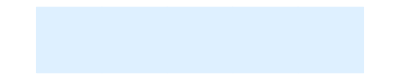

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,0}],{i,0,4}]}]]
```

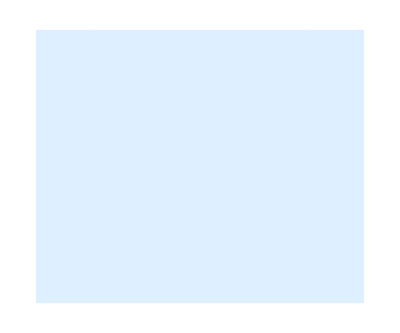

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,5}]}]]
```

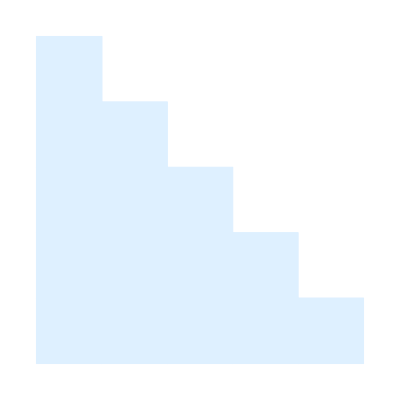

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}]}]]
```

```mathematica
Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}]//Grid
```

Rectangle[{0,4}] |  |  |  | 
Rectangle[{0,3}] | Rectangle[{1,3}] |  |  | 
Rectangle[{0,2}] | Rectangle[{1,2}] | Rectangle[{2,2}] |  | 
Rectangle[{0,1}] | Rectangle[{1,1}] | Rectangle[{2,1}] | Rectangle[{3,1}] | 
Rectangle[{0,0}] | Rectangle[{1,0}] | Rectangle[{2,0}] | Rectangle[{3,0}] | Rectangle[{4,0}]

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,5,9-j}]}]]
```

-Graphics-

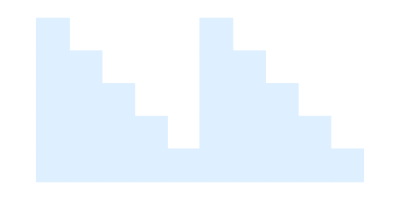

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Table[Rectangle[{i,j}],{j,4,0,-1},{i,5,9-j}]}]]
```

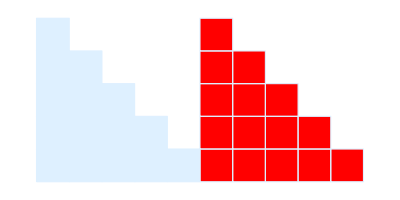

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,5,9-j}]}]]
```

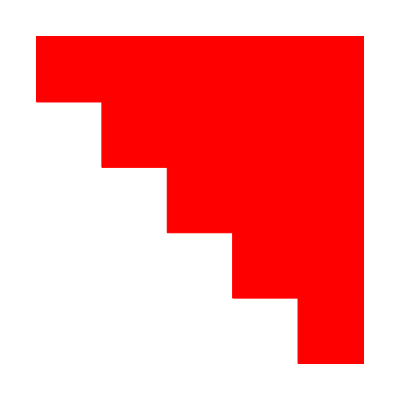

```mathematica
Graphics[Flatten[{EdgeForm[Thick],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,9-j,9}]}]]
```

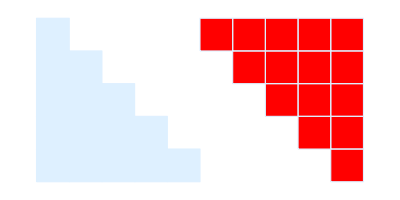

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,9-j,9}]}]]
```

```mathematica
Graphics[Flatten[{EdgeForm[Thick],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,5-j,5}]}]]
```

-Graphics-

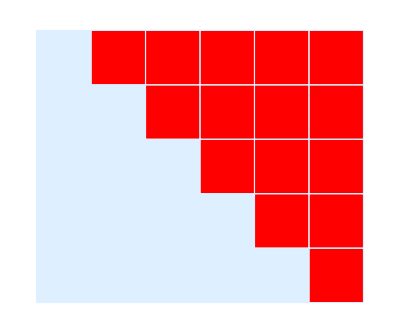

```mathematica
Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,5-j,5}]}]]
```

```mathematica
ListAnimate[{Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}]}]],"1+2+3+4+5"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Table[Rectangle[{i,j}],{j,4,0,-1},{i,5,9-j}]}]],"2*(1+2+3+4+5)"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,5,9-j}]}]],"2*(1+2+3+4+5)"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,9-j,9}]}]],"2*(1+2+3+4+5)"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}],Red,Table[Rectangle[{i,j}],{j,4,0,-1},{i,5-j,5}]}]],"5*(5+1)"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,5}]}]],"2*(1+2+3+4+5)=5*(5+1)"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}]}]],"1+2+3+4+5=5*(5+1)/2"],Labeled[Graphics[Flatten[{EdgeForm[Thick],LightBlue,Table[Rectangle[{i,j}],{j,4,0,-1},{i,0,4-j}]}]],"1+2+3+4+5=5*(5+1)/2=15"]}]
```